Figure out what power is clipped off when a 2D Gaussian beam of a given 1/e^2 diameter passes through an aperture of a given size

```mathematica
Clear["Global`*"];
```

```mathematica
gaussianbeam[x_,y_,waistradX_,waistradY_,totalpower_]:=2*totalpower/(Pi*waistradX*waistradY)*Exp[-2*x^2/waistradX^2]*Exp[-2*y^2/waistradY^2];
```

```mathematica
NIntegrate[gaussianbeam[x,y,17,17,20]*Boole[x^2+y^2≤50^2],{x,-70,70},{y,-70,70}]
```

20.

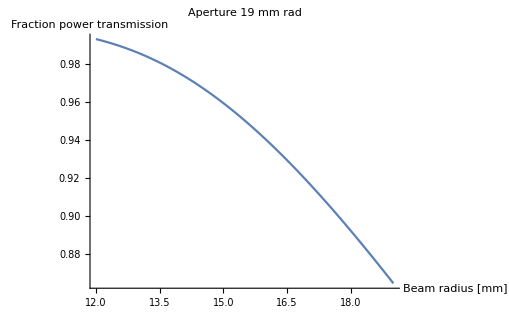

```mathematica
Plot[NIntegrate[gaussianbeam[x,y,beamRad,beamRad,20]*Boole[x^2+y^2≤19^2],{x,-70,70},{y,-70,70}]/20(*this is the total power*),{beamRad,12,19},AxesLabel->{"Beam radius [mm]","Fraction power transmission"},PlotLabel->"Aperture 19 mm rad"]
```